```mathematica
DSolve[g''[t]/g[t]==0,g[t],t]
```

{{g[t]→C[1]+t C[2]}}

```mathematica
{{g[t]->C[1]+t C[2]}}⟦1,1,2⟧
```

C[1]+t C[2]

```mathematica
DSolve[y''[x]/y[x]==(k^2),y[x],x]
```

{{y[x]→ⅇ^(k x) C[1]+ⅇ^(-k x) C[2]}}

```mathematica
DSolve[g''[t]/g[t]-Ρ*a*t==(k^2),g[t],t]
```

{{g[t]→AiryAi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[1]+AiryBi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[2]}}

```mathematica
{{g[t]->AiryAi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[1]+AiryBi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[2]}}⟦1,1,2⟧
```

AiryAi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[1]+AiryBi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[2]

```mathematica
FullSimplify[AiryAi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[1]+AiryBi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[2]]
```

AiryAi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[1]+AiryBi[(k^2+a t Ρ)/(a Ρ)^(2/3)] C[2]

```mathematica
k=17
a=20
Ρ=20
A1=1
B1=0
```

17

20

20

1

0

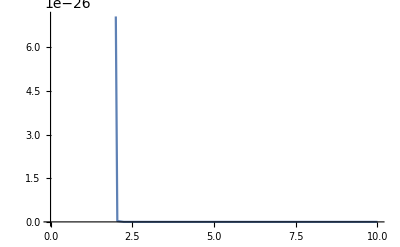

```mathematica
Plot[AiryAi[(k^2+a t Ρ)/(a Ρ)^(2/3)] A1+AiryBi[(k^2+a t Ρ)/(a Ρ)^(2/3)] B1,{t,0,10}]
```

```mathematica
N[AiryAi[1]]
```

0.135292

```mathematica
NDSolve[{y''[x]/y[x]==0,y[0]==0,y'[x]==1},y,{x,0,a}]
```

NDSolve::overdet: There are fewer dependent variables, {y[x]}, than equations, so the system is overdetermined.

NDSolve[{y''[x]/y[x]==0,y[0]==0,y'[x]==1},y,{x,0,a}]

```mathematica
xpp*y*z+x*ypp*z-vel*x*y*zpp==0//Simplify
```

```mathematica
xpp y z+x ypp z==vel x y zpp/(x*y)
```

```mathematica
(xpp y z+x ypp z)/(x*y)==vel zpp
```

(xpp y z+x ypp z)/(x y)==vel zpp

```mathematica
(xpp y z+x ypp z)/(x y)==vel zpp//Simplify
```

```mathematica
((xpp z)/x+(ypp z)/y)/z==vel zpp/z
```

```mathematica
((xpp z)/x+(ypp z)/y)/z==(vel zpp)/z//Simplify
```

(vel zpp)/z==xpp/x+ypp/y